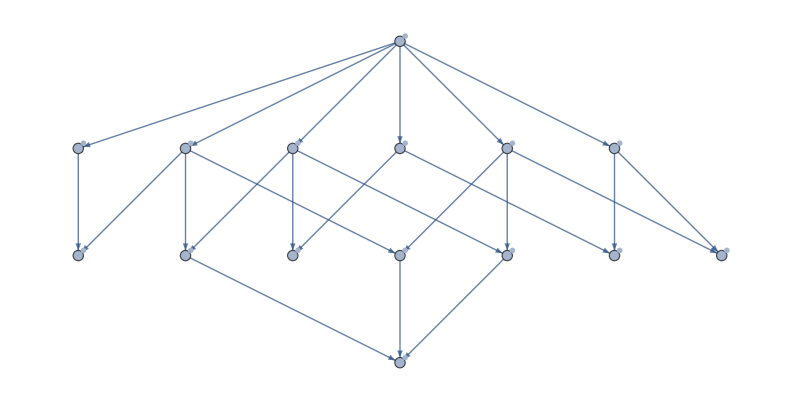

```mathematica
With [{g=SortGraph[ReadGrof[5]]},
With[{form=FindFullFormula[g]},
Graph[
FormulaGraphReverse2[form],
VertexLabels->
Map[#->ShowSolution[g,#,ImageSize->60]&,form],
ImageSize->800
]
]
]
```

```mathematica
EdgeList[SortGraph[ReadGrof[5]]]
```

{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->4,3<->5,3<->6,3<->7,4<->5,4<->6,5<->6,5<->7}

```mathematica
EdgeList[EdgeContract[SortGraph[ReadGrof[5]],2<->6]]//FindFullFormula4
```

{v15x2x3x47}

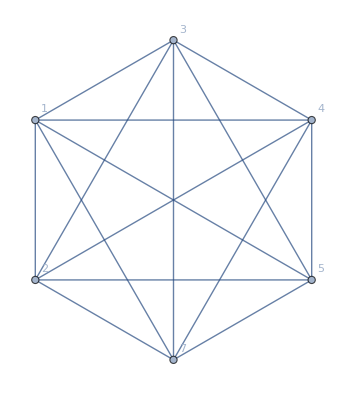

```mathematica
Graph[EdgeContract[SortGraph[ReadGrof[5]],2<->6]//MakeComplete,VertexLabels->"Name"]
```

```mathematica
MakeComplete[g_]:=Graph[VertexList[g],Table[UndirectedEdge[s[[1]],s[[2]]],{s,Subsets[VertexList[g],{2}]}]]
```

```mathematica
ShowSolution[g_,sol_, options:OptionsPattern[{ShowSolution,Graph}]]:=Block[{result=CompleteGraph[VertexCount[g]], colors=Association[],sorted, vertices=Association[]},
(* start with everything in gray *)
Table[
sorted=SortEdge[UndirectedEdge[couple[[1]],couple[[2]]]];
colors[sorted]=LightGray
,{couple,Subsets[VertexList[g],{2}]}
];
(* all missing edges in green *)
Table[
sorted=SortEdge[e];
colors[e]={Thick,Darker[Green]}
,
{e,EdgeList[GraphComplement[g]]}
];
(* all solution edges in red *)
Table[
If[Length[s]==1,
vertices[s[[1]]]=Red,
Table[
sorted=SortEdge[UndirectedEdge[couple[[1]],couple[[2]]]];
colors[sorted]={Thickness[0.03],Red}
,{couple,Subsets[s,{2}]}
]
]
,
{s,SymbolToSets[sol]}
];
Graph[MakeComplete[g],
VertexStyle->Normal[vertices],
EdgeStyle->Normal[colors],
options,
VertexLabels->"Name"
]
]
```

```mathematica
VertexList[EdgeContract[SortGraph[ReadGrof[5]],2<->6]]
```

{1,3,4,5,7,2}

```mathematica
ShowSolution[EdgeContract[SortGraph[ReadGrof[5]],2<->6],v15x2x3x47,ImageSize->60]
```

-Graphics-

```mathematica
CollectMPGEdges[SortGraph[ReadGrof[5]]]
```

{1<->2,1<->3,1<->7,2<->6,3<->4,4<->5,4<->6,5<->7}

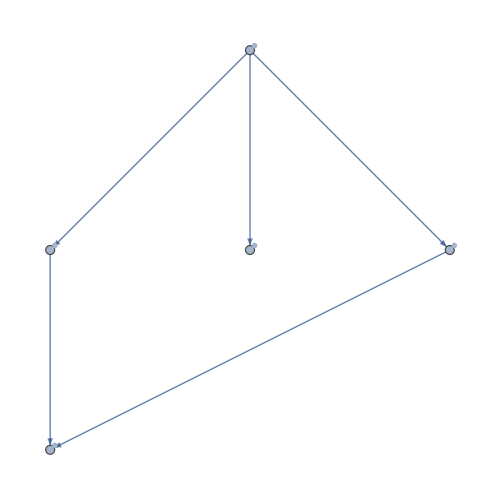
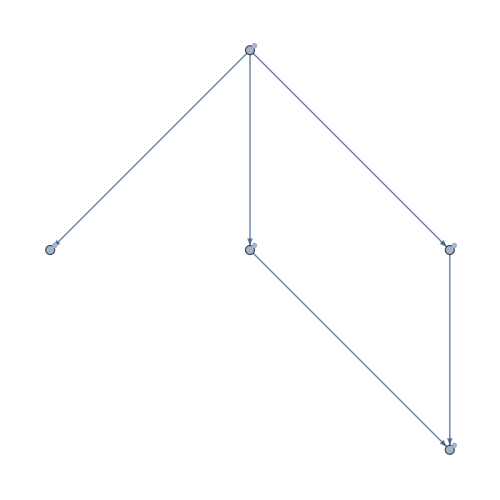
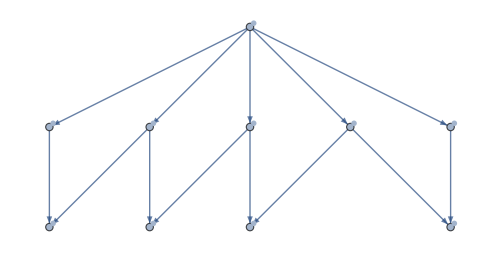
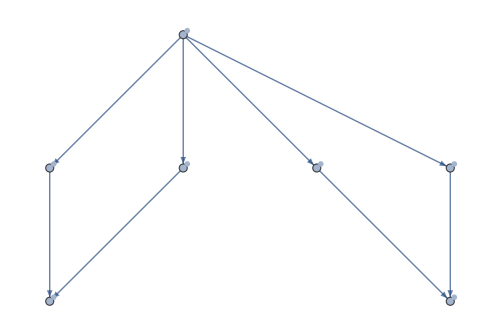
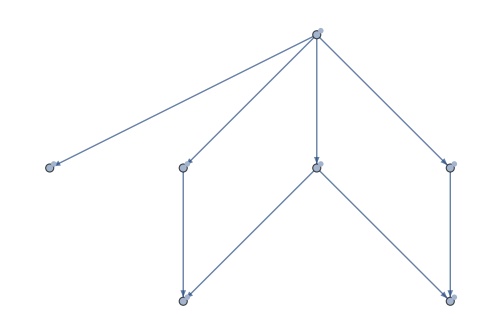
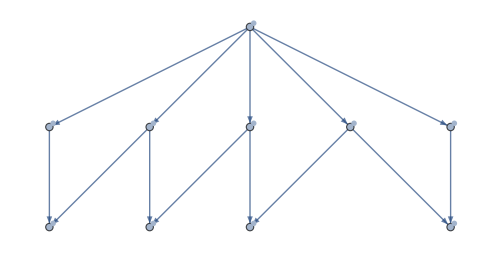
{-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->7,-Graphics-2<->3,-Graphics-2<->5,-Graphics-2<->6,-Graphics-2<->7,-Graphics-3<->4,-Graphics-3<->5,-Graphics-3<->6,-Graphics-3<->7,-Graphics-4<->5,-Graphics-4<->6,-Graphics-5<->6,-Graphics-5<->7}

```mathematica
With[{h=SortGraph[ReadGrof[5]]},
With[{mpg=CollectMPGEdges[h]},
Table[
With [{g=SortGraph[EdgeContract[h,e]]},
With[{form=FindFullFormula[g]},
Labeled[
Graph[
FormulaGraphReverse2[form],
VertexLabels->
Map[#->ShowSolution[g,#,ImageSize->60]&,form],
ImageSize->500
],
If[MemberQ[mpg,e],Style[e,Red],e]]
]
],{e,EdgeList[h]}]
]
]
```